```mathematica
EHCoefficient=Limit[-(hbar2 M^2 (1+ϵ)+hbar2 M^2 ϵ Log[μbar2/M^2])/(12ϵ),{ϵ->Infinity,hbar2->1/(16Pi^2)}]/M^2//Simplify
```

-(1+Log[μbar2/M^2])/(192 π^2)

```mathematica
cosmoConstantCoefficient = Limit[-(hbar2 M^4 (2+3 ϵ)+2 hbar2 M^4 ϵ Log[μbar2/M^2])/(8ϵ),{ϵ->Infinity,hbar2->1/(16Pi^2)}]/M^4//Simplify
```

-(3+2 Log[μbar2/M^2])/(128 π^2)

```mathematica
ricciSquaredCoefficient = Limit[((hbar2+hbar2 ϵ Log[μbar2/M^2])/(120 ϵ)),{ϵ->Infinity,hbar2->1/(16Pi^2)}]//Simplify
```

Log[μbar2/M^2]/(1920 π^2)

```mathematica
ricciScalarSquaredCoefficient = Limit[((hbar2+hbar2 ϵ Log[μbar2/M^2])/(240 ϵ)),{ϵ->Infinity,hbar2->1/(16Pi^2)}]//Simplify
```

Log[μbar2/M^2]/(3840 π^2)

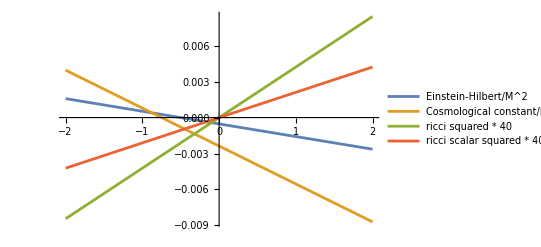

```mathematica
Plot[{EHCoefficient/.{μbar2->(Exp[t]M)^2},cosmoConstantCoefficient/.{μbar2->(Exp[t]M)^2},ricciSquaredCoefficient*40/.{μbar2->(Exp[t]M)^2},ricciScalarSquaredCoefficient*40/.{μbar2->(Exp[t]M)^2}},{t,-2,2},PlotLegends->{"Einstein-Hilbert/M^2","Cosmological constant/M^4","ricci squared * 40","ricci scalar squared * 40"}]
```

```mathematica
Solve[{M1^2+M2^2==R,M1^4+M2^4==Λ},{M1,M2}]
```

{{M1→-(√(R-√(-R^2+2 Λ)))/(√2),M2→-(√(R+√(-R^2+2 Λ)))/(√2)},{M1→-(√(R-√(-R^2+2 Λ)))/(√2),M2→(√(R+√(-R^2+2 Λ)))/(√2)},{M1→(√(R-√(-R^2+2 Λ)))/(√2),M2→-(√(R+√(-R^2+2 Λ)))/(√2)},{M1→(√(R-√(-R^2+2 Λ)))/(√2),M2→(√(R+√(-R^2+2 Λ)))/(√2)},{M1→-(√(R+√(-R^2+2 Λ)))/(√2),M2→-(√(R-√(-R^2+2 Λ)))/(√2)},{M1→-(√(R+√(-R^2+2 Λ)))/(√2),M2→(√(R-√(-R^2+2 Λ)))/(√2)},{M1→(√(R+√(-R^2+2 Λ)))/(√2),M2→-(√(R-√(-R^2+2 Λ)))/(√2)},{M1→(√(R+√(-R^2+2 Λ)))/(√2),M2→(√(R-√(-R^2+2 Λ)))/(√2)}}